## Analysis Functions

```mathematica
<< Units`
```

```mathematica
f[t_] := Exp[b t]
params = {b}
```

{b}

```mathematica
funs2={1,Log[t]}
params2={a,b}
g[t_]=Exp[params2.funs2]
```

{1,Log[t]}

{a,b}

ⅇ^(a+b Log[t])

```mathematica
GetParams2[expr_]:=Solve[(expr==funs2.params2)/.{{t->1},{t->2},{t->3}},params2]⟦1⟧
```

```mathematica
LinearisedFit=Function[{data,function,parameters,variable},
Module[{ldata},
ldata={#⟦1⟧,Log[#⟦2⟧]}&/@data;
GetParams2[Fit[data,funs2,t]]]]
```

Function[{data,function,parameters,variable},Module[{ldata},ldata=({#1⟦1⟧,Log[#1⟦2⟧]}&)/@data;GetParams2[Fit[data,funs2,t]]]]

```mathematica
AnalysePerf=Function[{id},
dataplot[id] = ListPlot[runtimes[id], Joined -> False, PlotStyle -> {Red, Thick}, Frame -> True];
fit[id] = FindFit[runtimes[id], f[t], params, t];
fitplot[id] = Plot[f[t] /. fit[id], {t, runtimes[id]⟦1,1⟧,runtimes[id]⟦-1,1⟧}, PlotStyle -> {Blue, Dashed}, Frame -> True,PlotRange->All];
GraphicsColumn[{
ListLogLogPlot[runtimes[id], Joined -> False, Frame -> True],
Show[{ fitplot[id],dataplot[id]}]}]];
```

```mathematica
AnalysePerfPoly=Function[{id},
dataplot[id] = ListPlot[runtimes[id], Joined -> False, PlotStyle -> {Red, Thick}, Frame -> True];
fit[id] = LinearisedFit[runtimes[id], g[t], params2, t];
fitplot[id] = Plot[f[t] /. fit[id], {t, runtimes[id]⟦1,1⟧,runtimes[id]⟦-1,1⟧}, PlotStyle -> {Blue, Dashed}, Frame -> True,PlotRange->All];
GraphicsColumn[{
ListLogLogPlot[runtimes[id], Joined -> False, Frame -> True],
Show[{ fitplot[id],dataplot[id]}]}]];
```

```mathematica
time[id_]:=(f[#]/.fit[id])Second&
```

## General CF algorithm

### Performance on SBCL

```mathematica
runtimes[sbcl]={{10, 0.004}, {20, 0.045}, {30, 0.45}, {40, 2.46}, {50, 9.249}, {60, 26.75}, {70, 90.57}, {80, 232.46}, {90, 527.5}}
```

{{10,0.004},{20,0.045},{30,0.45},{40,2.46},{50,9.249},{60,26.75},{70,90.57},{80,232.46},{90,527.5}}

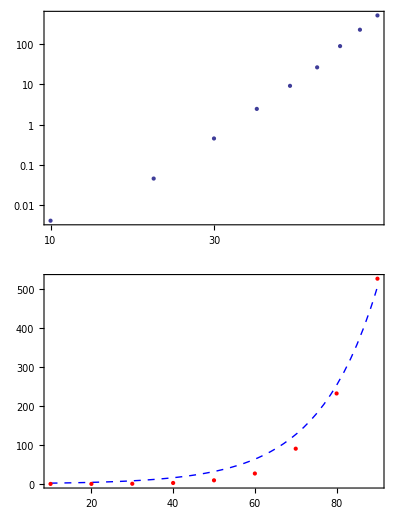

```mathematica
AnalysePerf[sbcl]
```

```mathematica
Convert[time[sbcl][250],Day]
```

377.598 Day

### Performance on CLISP

```mathematica
runtimes[clisp]={{10, 0.009}, {20, 0.028}, {30, 0.168}, {40, 0.956}, {50, 4.489135}, {60, 17.552}, {70, 60}, {80, 179.3}, {90, 752.7}}
```

{{10,0.009},{20,0.028},{30,0.168},{40,0.956},{50,4.48914},{60,17.552},{70,60},{80,179.3},{90,752.7}}

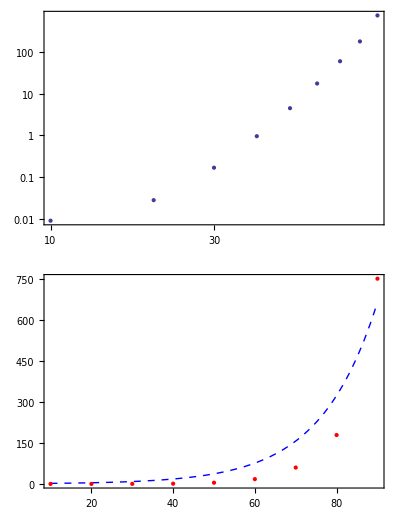

```mathematica
AnalysePerf[clisp]
```

```mathematica
Convert[time[clisp][250],Day]
```

0.0143127 Day

### Comparison

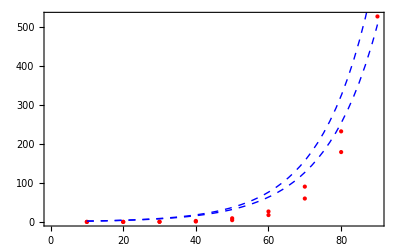

```mathematica
Show[{dataplot[sbcl],fitplot[sbcl],dataplot[clisp],fitplot[clisp]}]
```

## Square Root CF algorithm

### SBCL

```mathematica
runtimes[sqsbcl]={{10, 0.001}, {20, 0.005}, {30, 0.013}, {40, 0.028}, {50, 0.090}, {60, 0.115}, {70, 0.216}, {80, 0.281}, {90, 0.391}, {100, 0.643}, {110, 1.665}, {120, 2.067}, {130, 3.006}, {140, 5.115}, {150, 7.242}, {160, 12.291}, {170, 13.779}, {180, 24.258}, {190, 32.658}, {200, 43.904}}
runtimes[sqsbclasym]=Drop[runtimes[sqsbcl],10]
```

{{10,0.001},{20,0.005},{30,0.013},{40,0.028},{50,0.09},{60,0.115},{70,0.216},{80,0.281},{90,0.391},{100,0.643},{110,1.665},{120,2.067},{130,3.006},{140,5.115},{150,7.242},{160,12.291},{170,13.779},{180,24.258},{190,32.658},{200,43.904}}

{{110,1.665},{120,2.067},{130,3.006},{140,5.115},{150,7.242},{160,12.291},{170,13.779},{180,24.258},{190,32.658},{200,43.904}}

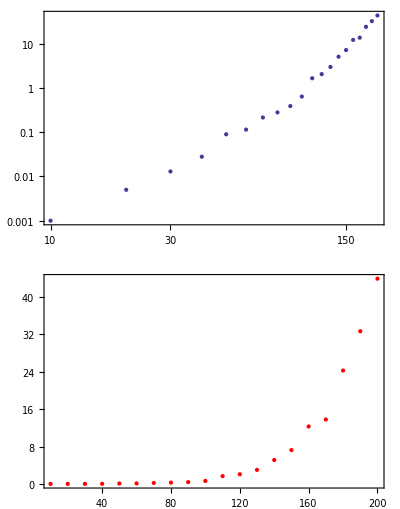

```mathematica
AnalysePerfPoly[sqsbcl]
```

```mathematica
fit[sqsbcl]
```

{a→-31.9909,b→8.91063}

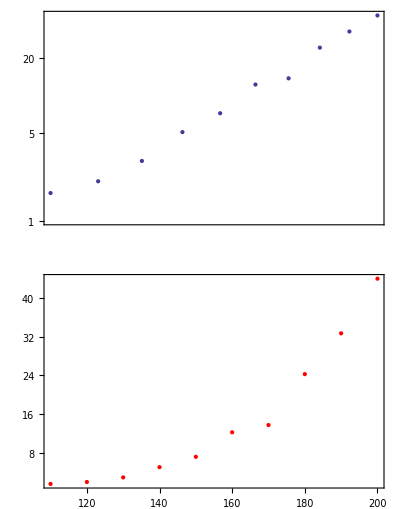

```mathematica
AnalysePerfPoly[sqsbclasym]
```

### CLISP

```mathematica
runtimes[sqclisp]={{10, 0.0017}, {20, 0.0057}, {30, 0.018}, {40, 0.24}, {50, 0.062}, {60, 0.126}, {70, 0.245}, {80, 0.505}, {90, 0.865}, {100, 1.556}, {110, 2.629}, {120, 4.243}, {130, 6.603}, {140, 10.49}, {150, 15.309}, {160, 22.21}, {170, 31.96}, {180, 44.553}, {190, 61.276}, {200, 81.40}}
runtimes[sqclispasym]=Drop[runtimes[sqclisp],10]
```

{{10,0.0017},{20,0.0057},{30,0.018},{40,0.24},{50,0.062},{60,0.126},{70,0.245},{80,0.505},{90,0.865},{100,1.556},{110,2.629},{120,4.243},{130,6.603},{140,10.49},{150,15.309},{160,22.21},{170,31.96},{180,44.553},{190,61.276},{200,81.4}}

{{110,2.629},{120,4.243},{130,6.603},{140,10.49},{150,15.309},{160,22.21},{170,31.96},{180,44.553},{190,61.276},{200,81.4}}

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

FindFit::nrlnum: The function value {Overflow[], Overflow[], Overflow[], Overflow[], Overflow[], Overflow[], Overflow[], Overflow[], Overflow[]} is not a list of real numbers with dimensions {9} at {b, a, c, d} = {-4.35527×10^21, 1.06694×10^21, -4.16001×10^-12, 1.}.

General::unfl: Underflow occurred in computation.

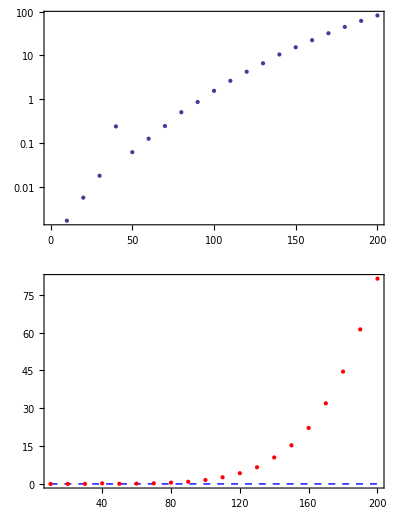

```mathematica
AnalysePerfPoly[sqclisp]
```

### Comparison

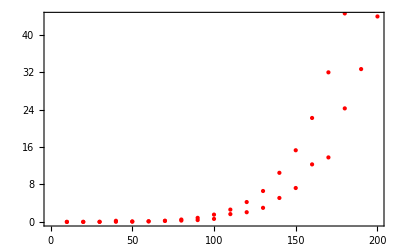

```mathematica
Show[{dataplot[sqsbcl],dataplot[sqclisp]}]
```

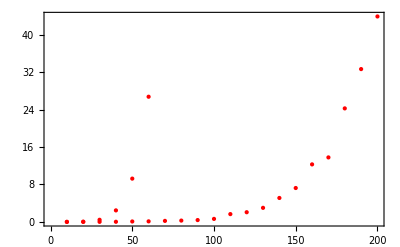

```mathematica
Show[{dataplot[sqsbcl],dataplot[sbcl]}]
```